Langevin

1.85195×10^-14 √((-Sin[348.703 √f]+Sinh[348.703 √f])/(√f (804248.-78.7594 f^2)^2 (-Cos[348.703 √f]+Cosh[348.703 √f])))

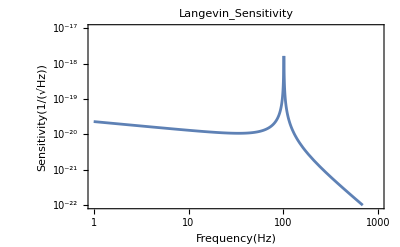

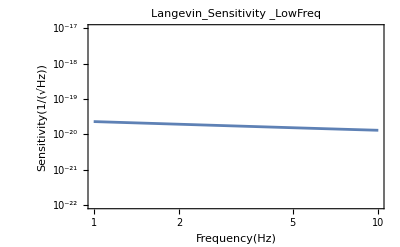

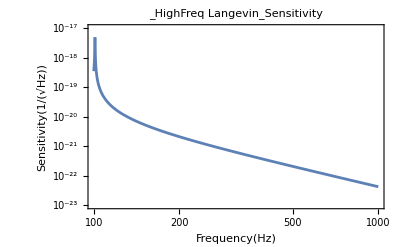

```mathematica
(*Langevin*)
LangevinPS=((s E0)/(s E0-M ω^2 L))^2(2 kB T^2 α^2 L^3)/κ 1/(kd L)(Sinh[2 kd L]-Sin[2 kd L])/(Cosh[2 kd L]-Cos[2 kd L])/.
{k2->√((ρ ω^2)/(s E0)),kd->√(ω/(2χ)),χ->κ/(ρ Cv)}/.
{kB->1.38 10^-23,T->300,α->5.0*10^(-6),L->0.35,κ->0.00008,ρ->0.008,Cv->7.9 10^2,ω->2π f,E0->4.0*10^(11),M->22.8/4,s->0.0016^2 Pi/4,χ->1.266*10^-5};
LangevinSensi=Sqrt[LangevinPS] / 200 / 3000
LangevinSensiG=LogLogPlot[LangevinSensi,{f,1,1000},PlotRange->{{1,1000},{10^-22,10^-17}},PlotLabel->Langevin_Sensitivity,Frame->True,FrameLabel->{Frequency[Hz],Sensitivity[1/Sqrt[Hz]]}]
(*Langevin Low Freq*)
LangevinSensiG10=LogLogPlot[LangevinSensi,{f,1,10},PlotRange->{{1,10},{10^-22,10^-17}},PlotLabel->Langevin_Sensitivity_LowFreq,Frame->True,FrameLabel->{Frequency[Hz],Sensitivity[1/Sqrt[Hz]]}]
(*Langevin High Freq*)
LangevinSensiG10=LogLogPlot[LangevinSensi,{f,100,1000},PlotRange->{{100,1000},{10^-23,10^-17}},PlotLabel->Langevin_Sensitivity_HighFreq,Frame->True,FrameLabel->{Frequency[Hz],Sensitivity[1/Sqrt[Hz]]}]
```